```mathematica
{hmpkill1np2,hmpkill10np2,hmpkill50np2,hmpkill90np2,hmpkill99np2,hmpkill1np3,hmpkill10np3,hmpkill50np3,hmpkill90np3,hmpkill99np3,hmpkill1np4,hmpkill10np4,hmpkill50np4,hmpkill90np4,hmpkill99np4,hmpkill1np5,hmpkill10np5,hmpkill50np5,hmpkill90np5,hmpkill99np5}=Import["C:\\Users\\mxy\\Desktop\\Modeling paper\\hmpnp2to5.mx"];
```

```mathematica
{hypkill1np2,hypkill10np2,hypkill50np2,hypkill90np2,hypkill99np2,hypkill1np3,hypkill10np3,hypkill50np3,hypkill90np3,hypkill99np3,hypkill1np4,hypkill10np4,hypkill50np4,hypkill90np4,hypkill99np4,hypkill1np5,hypkill10np5,hypkill50np5,hypkill90np5,hypkill99np5}=Import["C:\\Users\\mxy\\Desktop\\Modeling paper\\hypnp2to5.mx"];
```

```mathematica
{hmukill1np2,hmukill50np2,hmukill99np2,hmukill7000np2,hmukill14000np2,hmukill1np3,hmukill50np3,hmukill99np3,hmukill7000np3,hmukill14000np3,hmukill1np4,hmukill50np4,hmukill99np4,hmukill7000np4,hmukill14000np4,hmukill1np5,hmukill50np5,hmukill99np5,hmukill7000np5,hmukill14000np5}=Import["C:\\Users\\mxy\\Desktop\\Modeling paper\\hmunp2to5.mx"];
```

```mathematica
{hpkill1np2,hpkill50np2,hpkill99np2,hpkill3000np2,hpkill6000np2,hpkill1np3,hpkill50np3,hpkill99np3,hpkill3000np3,hpkill6000np3,hpkill1np4,hpkill50np4,hpkill99np4,hpkill3000np4,hpkill6000np4,hpkill1np5,hpkill50np5,hpkill99np5,hpkill3000np5,hpkill6000np5}=Import["C:\\Users\\mxy\\Desktop\\Modeling paper\\hpnp2to5.mx"];
```

```mathematica
{hptyp1np2,hptyp50np2,hptyp99np2,hptyp3000np2,hptyp6000np2,hptyp1np3,hptyp50np3,hptyp99np3,hptyp3000np3,hptyp6000np3,hptyp1np4,hptyp50np4,hptyp99np4,hptyp3000np4,hptyp6000np4,hptyp1np5,hptyp50np5,hptyp99np5,hptyp3000np5,hptyp6000np5}=Parallelize[{titeryieldproductivity[hpkill1np2],titeryieldproductivity[hpkill50np2],titeryieldproductivity[hpkill99np2],titeryieldproductivity[hpkill3000np2],titeryieldproductivity[hpkill6000np2],titeryieldproductivity[hpkill1np3],titeryieldproductivity[hpkill50np3],titeryieldproductivity[hpkill99np3],titeryieldproductivity[hpkill3000np3],titeryieldproductivity[hpkill6000np3],titeryieldproductivity[hpkill1np4],titeryieldproductivity[hpkill50np4],titeryieldproductivity[hpkill99np4],titeryieldproductivity[hpkill3000np4],titeryieldproductivity[hpkill6000np4],titeryieldproductivity[hpkill1np5],titeryieldproductivity[hpkill50np5],titeryieldproductivity[hpkill99np5],titeryieldproductivity[hpkill3000np5],titeryieldproductivity[hpkill6000np5]}]
```

```mathematica
{hpkill3000,hpkill6000,hptyp3000,hptyp6000}=Import["C:\\Users\\mxy\\Desktop\\Modeling paper\\hplargecorrect.mx"];
```

```mathematica
hpnp={{hptyp1[[4]]/oltyp[[4]],hptyp1np2[[4]]/oltyp[[4]],hptyp1np3[[4]]/oltyp[[4]],hptyp1np4[[4]]/oltyp[[4]],hptyp1np5[[4]]/oltyp[[4]]},{hptyp50[[4]]/oltyp[[4]],hptyp50np2[[4]]/oltyp[[4]],hptyp50np3[[4]]/oltyp[[4]],hptyp50np4[[4]]/oltyp[[4]],hptyp50np5[[4]]/oltyp[[4]]},{hptyp99[[4]]/oltyp[[4]],hptyp99np2[[4]]/oltyp[[4]],hptyp99np3[[4]]/oltyp[[4]],hptyp99np4[[4]]/oltyp[[4]],hptyp99np5[[4]]/oltyp[[4]]},{hptyp3000[[4]]/oltyp[[4]],hptyp3000np2[[4]]/oltyp[[4]],hptyp3000np3[[4]]/oltyp[[4]],hptyp3000np4[[4]]/oltyp[[4]],hptyp3000np5[[4]]/oltyp[[4]]},{hptyp6000[[4]]/oltyp[[4]],hptyp6000np2[[4]]/oltyp[[4]],hptyp6000np3[[4]]/oltyp[[4]],hptyp6000np4[[4]]/oltyp[[4]],hptyp6000np5[[4]]/oltyp[[4]]}}
```

{{1.33759,1.19454,1.09899,1.07268,1.0362},{1.61241,1.48503,1.41583,1.37979,1.33299},{1.91878,1.98622,2.01735,2.03266,2.0571},{3.5053,1.72651,0.933199,0.661479,0.545844},{2.38139,0.601448,0.372624,0.297778,0.265789}}

```mathematica
MatrixPlot[hpnp,ColorFunction->"RedBlueTones",PlotLegends->Automatic,FrameTicksStyle->Directive[Black, 16],PlotLegends->Automatic,LabelStyle->Directive[Black, 16]]
```

-Graphics-

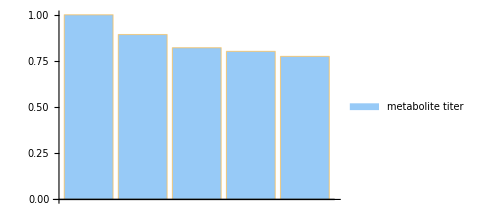

```mathematica
BarChart[{hptyp1[[4]]/hptyp1[[4]],hptyp1np2[[4]]/hptyp1[[4]],hptyp1np3[[4]]/hptyp1[[4]],hptyp1np4[[4]]/hptyp1[[4]],hptyp1np5[[4]]/hptyp1[[4]]},ChartLegends->{"metabolite titer"},ChartStyle->{RGBColor["#97caf7"]},AxesStyle->Directive[Black, 16],ImageSize->Medium]
```

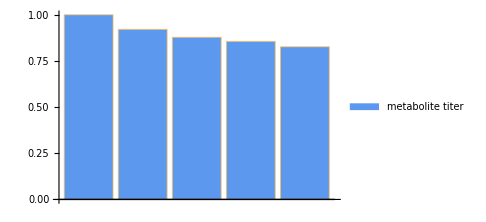

```mathematica
BarChart[{hptyp50[[4]]/hptyp50[[4]],hptyp50np2[[4]]/hptyp50[[4]],hptyp50np3[[4]]/hptyp50[[4]],hptyp50np4[[4]]/hptyp50[[4]],hptyp50np5[[4]]/hptyp50[[4]]},ChartLegends->{"metabolite titer"},ChartStyle->{RGBColor["#5c98ee"]},AxesStyle->Directive[Black, 16],ImageSize->Medium]
```

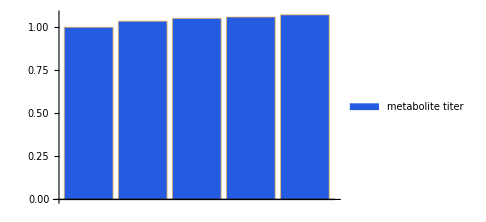

```mathematica
BarChart[{hptyp99[[4]]/hptyp99[[4]],hptyp99np2[[4]]/hptyp99[[4]],hptyp99np3[[4]]/hptyp99[[4]],hptyp99np4[[4]]/hptyp99[[4]],hptyp99np5[[4]]/hptyp99[[4]]},ChartLegends->{"metabolite titer"},ChartStyle->{
RGBColor["#245be1"]},AxesStyle->Directive[Black, 16],ImageSize->Medium]
```

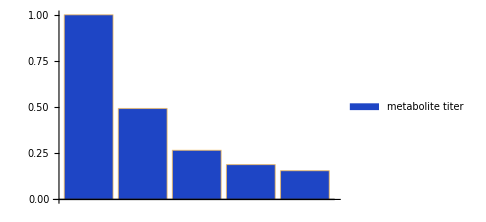

```mathematica
BarChart[{hptyp3000[[4]]/hptyp3000[[4]],hptyp3000np2[[4]]/hptyp3000[[4]],hptyp3000np3[[4]]/hptyp3000[[4]],hptyp3000np4[[4]]/hptyp3000[[4]],hptyp3000np5[[4]]/hptyp3000[[4]]},ChartLegends->{"metabolite titer"},ChartStyle->{
RGBColor["#1e45c5"]},AxesStyle->Directive[Black, 16],ImageSize->Medium]
```

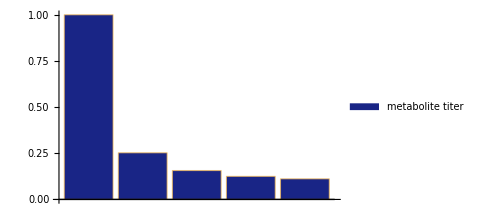

```mathematica
BarChart[{hptyp6000[[4]]/hptyp6000[[4]],hptyp6000np2[[4]]/hptyp6000[[4]],hptyp6000np3[[4]]/hptyp6000[[4]],hptyp6000np4[[4]]/hptyp6000[[4]],hptyp6000np5[[4]]/hptyp6000[[4]]},ChartLegends->{"metabolite titer"},ChartStyle->{
RGBColor["#192586"]},AxesStyle->Directive[Black, 16],ImageSize->Medium]
```

```mathematica
{hmutyp1np2,hmutyp50np2,hmutyp99np2,hmutyp7000np2,hmutyp14000np2,hmutyp1np3,hmutyp50np3,hmutyp99np3,hmutyp7000np3,hmutyp14000np3,hmutyp1np4,hmutyp50np4,hmutyp99np4,hmutyp7000np4,hmutyp14000np4,hmutyp1np5,hmutyp50np5,hmutyp99np5,hmutyp7000np5,hmutyp14000np5}=Parallelize[{titeryieldproductivity[hmukill1np2],titeryieldproductivity[hmukill50np2],titeryieldproductivity[hmukill99np2],titeryieldproductivity[hmukill7000np2],titeryieldproductivity[hmukill14000np2],titeryieldproductivity[hmukill1np3],titeryieldproductivity[hmukill50np3],titeryieldproductivity[hmukill99np3],titeryieldproductivity[hmukill7000np3],titeryieldproductivity[hmukill14000np3],titeryieldproductivity[hmukill1np4],titeryieldproductivity[hmukill50np4],titeryieldproductivity[hmukill99np4],titeryieldproductivity[hmukill7000np4],titeryieldproductivity[hmukill14000np4],titeryieldproductivity[hmukill1np5],titeryieldproductivity[hmukill50np5],titeryieldproductivity[hmukill99np5],titeryieldproductivity[hmukill7000np5],titeryieldproductivity[hmukill14000np5]}]
```

{1}
 |  |  |  |

```mathematica
{hmugen1,hmugen10,hmugen50,hmugen90,hmugen99,hmukeep1,hmukeep10,hmukeep50,hmukeep90,hmukeep99,hmumem1,hmumem10,hmumem50,hmumem90,hmumem99,hmukill1,hmukill10,hmukill50,hmukill90,hmukill99,hmutyp1,hmutyp10,hmutyp50,hmutyp90,hmutyp99}=Import["C:\\Users\\mxy\\Desktop\\Modeling paper\\hmu500c24hpercent.mx"];
```

```mathematica
hmutyp7000=titeryieldproductivity[hmukill7000];
```

```mathematica
hmutyp14000=titeryieldproductivity[hmukill14000];
```

```mathematica
hmunp={{hmutyp1[[4]]/oltyp[[4]],hmutyp1np2[[4]]/oltyp[[4]],hmutyp1np3[[4]]/oltyp[[4]],hmutyp1np4[[4]]/oltyp[[4]],hmutyp1np5[[4]]/oltyp[[4]]},{hmutyp50[[4]]/oltyp[[4]],hmutyp50np2[[4]]/oltyp[[4]],hmutyp50np3[[4]]/oltyp[[4]],hmutyp50np4[[4]]/oltyp[[4]],hmutyp50np5[[4]]/oltyp[[4]]},{hmutyp99[[4]]/oltyp[[4]],hmutyp99np2[[4]]/oltyp[[4]],hmutyp99np3[[4]]/oltyp[[4]],hmutyp99np4[[4]]/oltyp[[4]],hmutyp99np5[[4]]/oltyp[[4]]},{hmutyp7000[[4]]/oltyp[[4]],hmutyp7000np2[[4]]/oltyp[[4]],hmutyp7000np3[[4]]/oltyp[[4]],hmutyp7000np4[[4]]/oltyp[[4]],hmutyp7000np5[[4]]/oltyp[[4]]},{hmutyp14000[[4]]/oltyp[[4]],hmutyp14000np2[[4]]/oltyp[[4]],hmutyp14000np3[[4]]/oltyp[[4]],hmutyp14000np4[[4]]/oltyp[[4]],hmutyp14000np5[[4]]/oltyp[[4]]}}
```

{{1.54603,1.36775,1.26045,1.21903,1.1665},{1.73094,1.65084,1.58303,1.54873,1.5152},{1.92589,2.02277,2.10594,2.1877,2.2396},{1.97934,0.340818,0.23335,0.216647,0.2145},{0.742315,0.241506,0.215792,0.214338,0.213952}}

```mathematica
MatrixPlot[hmunp,ColorFunction->"AvocadoColors",PlotLegends->Automatic,FrameTicksStyle->Directive[Black, 16],PlotLegends->Automatic,LabelStyle->Directive[Black, 16]]
```

-Graphics-

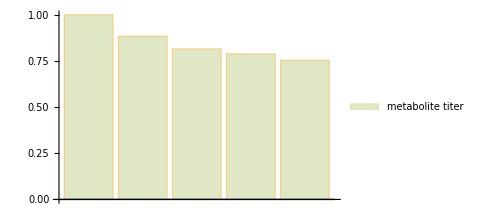

```mathematica
BarChart[{hmutyp1[[4]]/hmutyp1[[4]],hmutyp1np2[[4]]/hmutyp1[[4]],hmutyp1np3[[4]]/hmutyp1[[4]],hmutyp1np4[[4]]/hmutyp1[[4]],hmutyp1np5[[4]]/hmutyp1[[4]]},ChartLegends->{"metabolite titer"},ChartStyle->{RGBColor["#dfe7c5"]},AxesStyle->Directive[Black, 16],ImageSize->Medium]
```

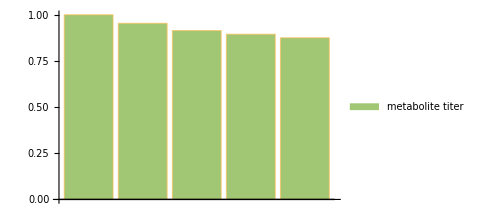

```mathematica
BarChart[{hmutyp50[[4]]/hmutyp50[[4]],hmutyp50np2[[4]]/hmutyp50[[4]],hmutyp50np3[[4]]/hmutyp50[[4]],hmutyp50np4[[4]]/hmutyp50[[4]],hmutyp50np5[[4]]/hmutyp50[[4]]},ChartLegends->{"metabolite titer"},ChartStyle->{RGBColor["#a1c774"]},AxesStyle->Directive[Black, 16],ImageSize->Medium]
```

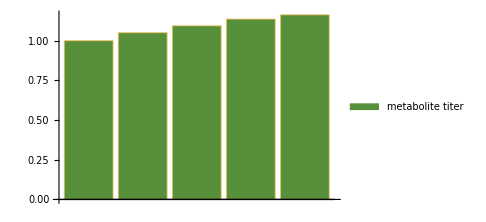

```mathematica
BarChart[{hmutyp99[[4]]/hmutyp99[[4]],hmutyp99np2[[4]]/hmutyp99[[4]],hmutyp99np3[[4]]/hmutyp99[[4]],hmutyp99np4[[4]]/hmutyp99[[4]],hmutyp99np5[[4]]/hmutyp99[[4]]},ChartLegends->{"metabolite titer"},ChartStyle->{RGBColor["#56903a"]},AxesStyle->Directive[Black, 16],ImageSize->Medium]
```

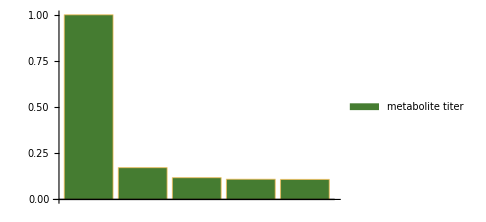

```mathematica
BarChart[{hmutyp7000[[4]]/hmutyp7000[[4]],hmutyp7000np2[[4]]/hmutyp7000[[4]],hmutyp7000np3[[4]]/hmutyp7000[[4]],hmutyp7000np4[[4]]/hmutyp7000[[4]],hmutyp7000np5[[4]]/hmutyp7000[[4]]},ChartLegends->{"metabolite titer"},ChartStyle->{RGBColor["#457c31"]},AxesStyle->Directive[Black, 16],ImageSize->Medium]
```

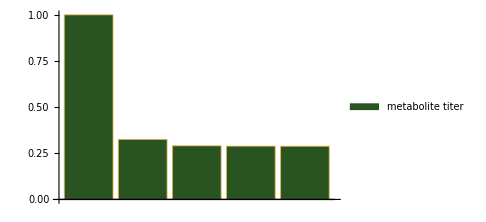

```mathematica
BarChart[{hmutyp14000[[4]]/hmutyp14000[[4]],hmutyp14000np2[[4]]/hmutyp14000[[4]],hmutyp14000np3[[4]]/hmutyp14000[[4]],hmutyp14000np4[[4]]/hmutyp14000[[4]],hmutyp14000np5[[4]]/hmutyp14000[[4]]},ChartLegends->{"metabolite titer"},ChartStyle->{RGBColor["#295421"]},AxesStyle->Directive[Black, 16],ImageSize->Medium]
```

```mathematica
{hyptyp1np2,hyptyp10np2,hyptyp50np2,hyptyp90np2,hyptyp99np2,hyptyp1np3,hyptyp10np3,hyptyp50np3,hyptyp90np3,hyptyp99np3,hyptyp1np4,hyptyp10np4,hyptyp50np4,hyptyp90np4,hyptyp99np4,hyptyp1np5,hyptyp10np5,hyptyp50np5,hyptyp90np5,hyptyp99np5}=Parallelize[{titeryieldproductivity[hypkill1np2],titeryieldproductivity[hypkill10np2],titeryieldproductivity[hypkill50np2],titeryieldproductivity[hypkill90np2],titeryieldproductivity[hypkill99np2],titeryieldproductivity[hypkill1np3],titeryieldproductivity[hypkill10np3],titeryieldproductivity[hypkill50np3],titeryieldproductivity[hypkill90np3],titeryieldproductivity[hypkill99np3],titeryieldproductivity[hypkill1np4],titeryieldproductivity[hypkill10np4],titeryieldproductivity[hypkill50np4],titeryieldproductivity[hypkill90np4],titeryieldproductivity[hypkill99np4],titeryieldproductivity[hypkill1np5],titeryieldproductivity[hypkill10np5],titeryieldproductivity[hypkill50np5],titeryieldproductivity[hypkill90np5],titeryieldproductivity[hypkill99np5]}];
```

```mathematica
{hypgen1,hypgen10,hypgen50,hypgen90,hypgen99,hypkeep1,hypkeep10,hypkeep50,hypkeep90,hypkeep99,hypmem1,hypmem10,hypmem50,hypmem90,hypmem99,hypkill1,hypkill10,hypkill50,hypkill90,hypkill99,hyptyp1,hyptyp10,hyptyp50,hyptyp90,hyptyp99}=Import["C:\\Users\\mxy\\Desktop\\Modeling paper\\hyp500c24hpercent.mx"];
```

```mathematica
hypnpm={{hyptyp1[[4]]/oltyp[[4]],hyptyp1np2[[4]]/oltyp[[4]],hyptyp1np3[[4]]/oltyp[[4]],hyptyp1np4[[4]]/oltyp[[4]],hyptyp1np5[[4]]/oltyp[[4]]},{hyptyp10[[4]]/oltyp[[4]],hyptyp10np2[[4]]/oltyp[[4]],hyptyp10np3[[4]]/oltyp[[4]],hyptyp10np4[[4]]/oltyp[[4]],hyptyp10np5[[4]]/oltyp[[4]]},{hyptyp50[[4]]/oltyp[[4]],hyptyp50np2[[4]]/oltyp[[4]],hyptyp50np3[[4]]/oltyp[[4]],hyptyp50np4[[4]]/oltyp[[4]],hyptyp50np5[[4]]/oltyp[[4]]},{hyptyp90[[4]]/oltyp[[4]],hyptyp90np2[[4]]/oltyp[[4]],hyptyp90np3[[4]]/oltyp[[4]],hyptyp90np4[[4]]/oltyp[[4]],hyptyp90np5[[4]]/oltyp[[4]]},{hyptyp99[[4]]/oltyp[[4]],hyptyp99np2[[4]]/oltyp[[4]],hyptyp99np3[[4]]/oltyp[[4]],hyptyp99np4[[4]]/oltyp[[4]],hyptyp99np5[[4]]/oltyp[[4]]}}
```

{{1.02408,1.01302,1.00968,1.0203,1.00625},{1.00467,1.01354,1.00671,1.01361,1.01928},{1.00604,0.99714,0.988145,1.00675,1.01251},{1.00369,0.991031,0.984975,0.978542,0.937213},{0.984732,0.897441,0.916108,0.843441,0.790819}}

```mathematica
MatrixPlot[hypnpm,ColorFunction->"GreenPinkTones",PlotLegends->{{0.85,1.0,0.05}},FrameTicksStyle->Directive[Black, 16],PlotLegends->Automatic,LabelStyle->Directive[Black, 16]]
```

-Graphics-

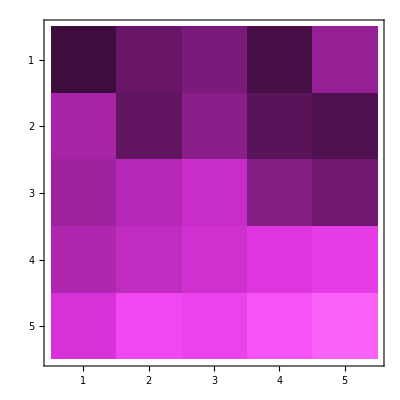

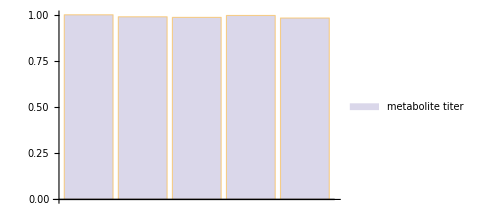

```mathematica
BarChart[{hyptyp1[[4]]/hyptyp1[[4]],hyptyp1np2[[4]]/hyptyp1[[4]],hyptyp1np3[[4]]/hyptyp1[[4]],hyptyp1np4[[4]]/hyptyp1[[4]],hyptyp1np5[[4]]/hyptyp1[[4]]},ChartLegends->{"metabolite titer"},ChartStyle->{RGBColor["#dad7ea"]},AxesStyle->Directive[Black, 16],ImageSize->Medium]
```

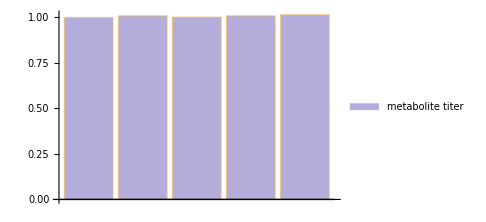

```mathematica
BarChart[{hyptyp10[[4]]/hyptyp10[[4]],hyptyp10np2[[4]]/hyptyp10[[4]],hyptyp10np3[[4]]/hyptyp10[[4]],hyptyp10np4[[4]]/hyptyp10[[4]],hyptyp10np5[[4]]/hyptyp10[[4]]},ChartLegends->{"metabolite titer"},ChartStyle->{RGBColor["#b4acdb"]},AxesStyle->Directive[Black, 16],ImageSize->Medium]
```

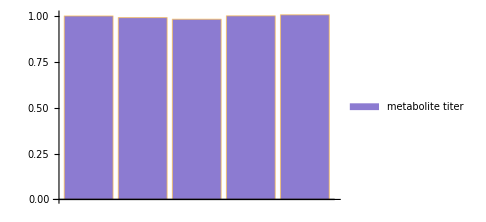

```mathematica
BarChart[{hyptyp50[[4]]/hyptyp50[[4]],hyptyp50np2[[4]]/hyptyp50[[4]],hyptyp50np3[[4]]/hyptyp50[[4]],hyptyp50np4[[4]]/hyptyp50[[4]],hyptyp50np5[[4]]/hyptyp50[[4]]},ChartLegends->{"metabolite titer"},ChartStyle->{RGBColor["#8c7bd1"]},AxesStyle->Directive[Black, 16],ImageSize->Medium]
```

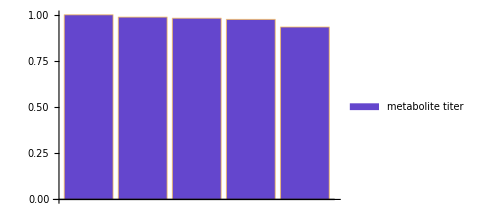

```mathematica
BarChart[{hyptyp90[[4]]/hyptyp90[[4]],hyptyp90np2[[4]]/hyptyp90[[4]],hyptyp90np3[[4]]/hyptyp90[[4]],hyptyp90np4[[4]]/hyptyp90[[4]],hyptyp90np5[[4]]/hyptyp90[[4]]},ChartLegends->{"metabolite titer"},ChartStyle->{RGBColor["#6446cd"]},AxesStyle->Directive[Black, 16],ImageSize->Medium]
```

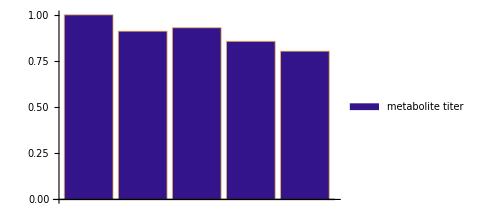

```mathematica
BarChart[{hyptyp99[[4]]/hyptyp99[[4]],hyptyp99np2[[4]]/hyptyp99[[4]],hyptyp99np3[[4]]/hyptyp99[[4]],hyptyp99np4[[4]]/hyptyp99[[4]],hyptyp99np5[[4]]/hyptyp99[[4]]},ChartLegends->{"metabolite titer"},ChartStyle->{RGBColor["#33148a"]},AxesStyle->Directive[Black, 16],ImageSize->Medium]
```

```mathematica
{hmptyp1np2,hmptyp10np2,hmptyp50np2,hmptyp90np2,hmptyp99np2,hmptyp1np3,hmptyp10np3,hmptyp50np3,hmptyp90np3,hmptyp99np3,hmptyp1np4,hmptyp10np4,hmptyp50np4,hmptyp90np4,hmptyp99np4,hmptyp1np5,hmptyp10np5,hmptyp50np5,hmptyp90np5,hmptyp99np5}=Parallelize[{titeryieldproductivity[hmpkill1np2],titeryieldproductivity[hmpkill10np2],titeryieldproductivity[hmpkill50np2],titeryieldproductivity[hmpkill90np2],titeryieldproductivity[hmpkill99np2],titeryieldproductivity[hmpkill1np3],titeryieldproductivity[hmpkill10np3],titeryieldproductivity[hmpkill50np3],titeryieldproductivity[hmpkill90np3],titeryieldproductivity[hmpkill99np3],titeryieldproductivity[hmpkill1np4],titeryieldproductivity[hmpkill10np4],titeryieldproductivity[hmpkill50np4],titeryieldproductivity[hmpkill90np4],titeryieldproductivity[hmpkill99np4],titeryieldproductivity[hmpkill1np5],titeryieldproductivity[hmpkill10np5],titeryieldproductivity[hmpkill50np5],titeryieldproductivity[hmpkill90np5],titeryieldproductivity[hmpkill99np5]}];
```

```mathematica
{hmpgen1,hmpgen10,hmpgen50,hmpgen90,hmpgen99,hmpkeep1,hmpkeep10,hmpkeep50,hmpkeep90,hmpkeep99,hmpmem1,hmpmem10,hmpmem50,hmpmem90,hmpmem99,hmpkill1,hmpkill10,hmpkill50,hmpkill90,hmpkill99,hmptyp1,hmptyp10,hmptyp50,hmptyp90,hmptyp99}=Import["C:\\Users\\mxy\\Desktop\\Modeling paper\\hmp500c24hpercent.mx"];
```

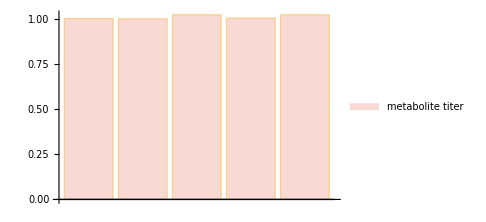

```mathematica
BarChart[{hmptyp1[[4]]/hmptyp1[[4]],hmptyp1np2[[4]]/hmptyp1[[4]],hmptyp1np3[[4]]/hmptyp1[[4]],hmptyp1np4[[4]]/hmptyp1[[4]],hmptyp1np5[[4]]/hmptyp1[[4]]},ChartLegends->{"metabolite titer"},ChartStyle->{RGBColor["#f8d9d3"]},AxesStyle->Directive[Black, 16],ImageSize->Medium]
```

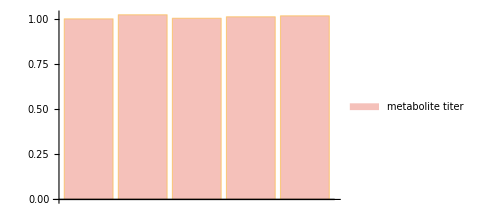

```mathematica
BarChart[{hmptyp10[[4]]/hmptyp10[[4]],hmptyp10np2[[4]]/hmptyp10[[4]],hmptyp10np3[[4]]/hmptyp10[[4]],hmptyp10np4[[4]]/hmptyp10[[4]],hmptyp10np5[[4]]/hmptyp10[[4]]},ChartLegends->{"metabolite titer"},ChartStyle->{RGBColor["#f5c1ba"]},AxesStyle->Directive[Black, 16],ImageSize->Medium]
```

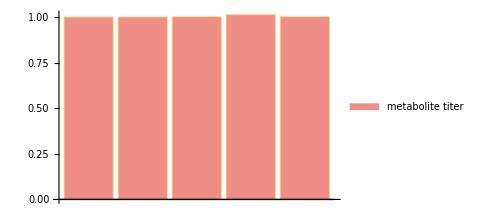

```mathematica
BarChart[{hmptyp50[[4]]/hmptyp50[[4]],hmptyp50np2[[4]]/hmptyp50[[4]],hmptyp50np3[[4]]/hmptyp50[[4]],hmptyp50np4[[4]]/hmptyp50[[4]],hmptyp50np5[[4]]/hmptyp50[[4]]},ChartLegends->{"metabolite titer"},ChartStyle->{RGBColor["#ef8d87"]},AxesStyle->Directive[Black, 16],ImageSize->Medium]
```

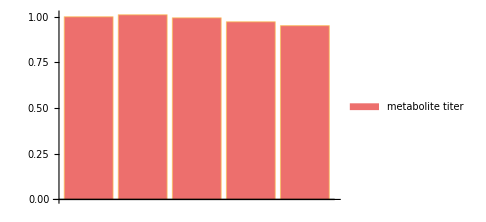

```mathematica
BarChart[{hmptyp90[[4]]/hmptyp90[[4]],hmptyp90np2[[4]]/hmptyp90[[4]],hmptyp90np3[[4]]/hmptyp90[[4]],hmptyp90np4[[4]]/hmptyp90[[4]],hmptyp90np5[[4]]/hmptyp90[[4]]},ChartLegends->{"metabolite titer"},ChartStyle->{RGBColor["#ed6f6d"]},AxesStyle->Directive[Black, 16],ImageSize->Medium]
```

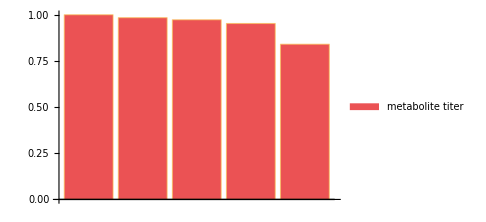

```mathematica
BarChart[{hmptyp99[[4]]/hmptyp99[[4]],hmptyp99np2[[4]]/hmptyp99[[4]],hmptyp99np3[[4]]/hmptyp99[[4]],hmptyp99np4[[4]]/hmptyp99[[4]],hmptyp99np5[[4]]/hmptyp99[[4]]},ChartLegends->{"metabolite titer"},ChartStyle->{RGBColor["#eb5254"]},AxesStyle->Directive[Black, 16],ImageSize->Medium]
```

```mathematica
hmpnpm={{hmptyp1[[4]]/oltyp[[4]],hmptyp1np2[[4]]/oltyp[[4]],hmptyp1np3[[4]]/oltyp[[4]],hmptyp1np4[[4]]/oltyp[[4]],hmptyp1np5[[4]]/oltyp[[4]]},{hmptyp10[[4]]/oltyp[[4]],hmptyp10np2[[4]]/oltyp[[4]],hmptyp10np3[[4]]/oltyp[[4]],hmptyp10np4[[4]]/oltyp[[4]],hmptyp10np5[[4]]/oltyp[[4]]},{hmptyp50[[4]]/oltyp[[4]],hmptyp50np2[[4]]/oltyp[[4]],hmptyp50np3[[4]]/oltyp[[4]],hmptyp50np4[[4]]/oltyp[[4]],hmptyp50np5[[4]]/oltyp[[4]]},{hmptyp90[[4]]/oltyp[[4]],hmptyp90np2[[4]]/oltyp[[4]],hmptyp90np3[[4]]/oltyp[[4]],hmptyp90np4[[4]]/oltyp[[4]],hmptyp90np5[[4]]/oltyp[[4]]},{hmptyp99[[4]]/oltyp[[4]],hmptyp99np2[[4]]/oltyp[[4]],hmptyp99np3[[4]]/oltyp[[4]],hmptyp99np4[[4]]/oltyp[[4]],hmptyp99np5[[4]]/oltyp[[4]]}}
```

{{1.00601,1.00442,1.02687,1.009,1.02677},{0.99639,1.01885,0.999645,1.00777,1.0131},{0.999772,0.999897,1.00124,1.01289,1.00132},{1.00084,1.01177,0.995011,0.973409,0.952194},{0.99678,0.981061,0.969761,0.949767,0.837853}}

```mathematica
MatrixPlot[hmpnpm,ColorFunction->"ThermometerColors",PlotLegends->Automatic,FrameTicksStyle->Directive[Black, 16],PlotLegends->Automatic,LabelStyle->Directive[Black, 16]]
```

-Graphics-